```mathematica
OptionsFor2[g_,vertices_]:=Block[
{result={}, 
graph2, graph2Bis, graph3, graph3Bis,
sols,
div, secondBis, second, third,thirdBis, 
vert2, vert2Bis,  vert3, vert3Bis, circle = Rule3Cycle[vertices], newNode, toAdd},

div=ChromaticPolynomial[g,4]/24;
newNode=Max[VertexList[g]]+1;
toAdd=Table[newNode<->vertex,{vertex,vertices}];

vert2={vertices[[3]]<->vertices[[5]],vertices[[3]]<->vertices[[1]]};
graph2=Graph[EdgeAdd[g,vert2]];
second=(ChromaticPolynomial[graph2,4]/24);

vert2Bis={vertices[[1]]<->vertices[[3]],vertices[[1]]<->vertices[[4]]};
graph2Bis=Graph[EdgeAdd[g,vert2Bis]];
secondBis=(ChromaticPolynomial[graph2Bis,4]/24);

vert3={vertices[[4]]<->vertices[[1]]};
graph3=Graph[EdgeAdd[g,vert3]];
third=(ChromaticPolynomial[graph3,4]/24);

vert3Bis={vertices[[3]]<->vertices[[5]]};
graph3Bis=Graph[EdgeAdd[g,vert3Bis]];
thirdBis=(ChromaticPolynomial[graph3Bis,4]/24);

result={second+ secondBis, third+ thirdBis}/div
]
```

```mathematica
deps3=ReadList["D:\\Grofs\\dependencies3.txt",Expression];Length[deps3]
```

2436995

```mathematica
Length[deps3]
```

100

```mathematica
ListPlot[
Monitor[

Table[
With[
{empty=EdgeDelete[ReadGrof[deps3[[k,1]]],deps3[[k,3,3]]],cycle=deps3[[k,3,2]]},
OptionsFor2[empty, deps3[[k,3,2]]]
],{k,1,1000000}],k]
]
```

$Aborted

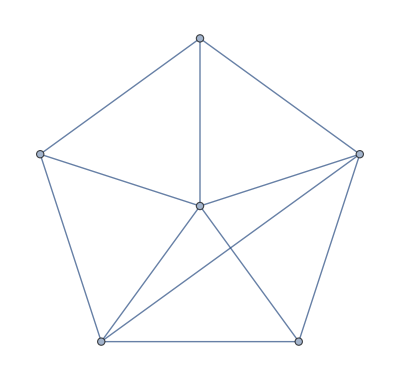

```mathematica
fault=EdgeAdd[WheelGraph[6],2<->4]
```

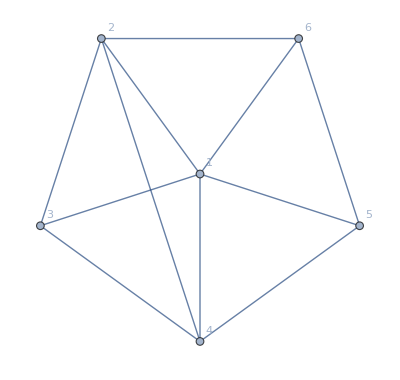

```mathematica
Graph[fault, VertexLabels->"Name", GraphLayout->"RadialEmbedding"]
```

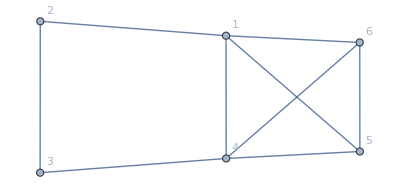

```mathematica
Graph[Rule1[fault,1,4,5], VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding"]
```

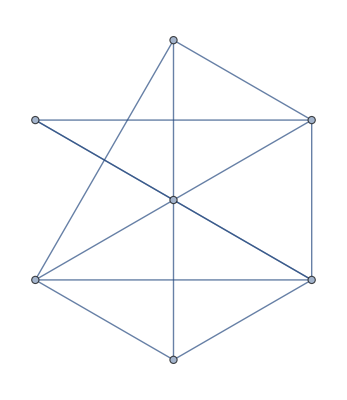

```mathematica
Rule1[fault,1,4,5]
```

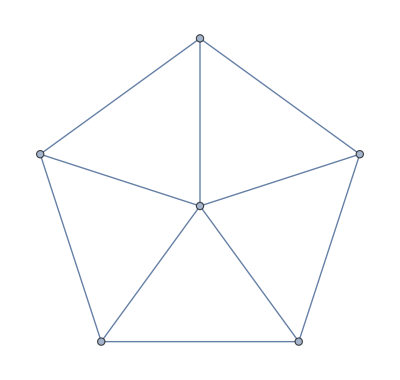

```mathematica
GraphWheelGraph[6]
```